```mathematica
Diffusion On the Surface of a Sphere
Christian Warren
Math299M
```

Diffusion is the spreading out of something. This is a fundamental process with application to topics as diverse as physics and finance.

We can simulate diffusion with “Random Walkers.”  Imagine a bunch of drunk college students walking up and down the street changing direction at random.

```mathematica
walk[]:=Module[{pnts= {},x=0, nsteps=1000},
For[i=0,i<nsteps,i++,
r=RandomReal[];
(* if "heads" go "left", if "tails" go "right" *)
If[r<0.5,x=x+1,x=x-1];
AppendTo[pnts,x]];
pnts]
```

Here is a series of random walkers. Initially, everyone is bunched together, but over time everyone spreads out.

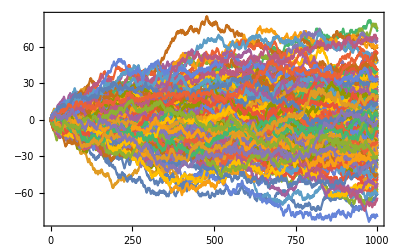

```mathematica
walks = Table[walk[], {i, 200}]; 
ListLinePlot[walks, Frame -> True]
```

This process is described by the diffusion equation
∂_t u = D∇^2 u
Where D is the diffusion coefficient. We will set this to 1. In one dimension the solution to the diffusion equation is a simple Gaussian. Note the numerical instability near t = 0.

```mathematica
pdf[x_,t_]:=Module[{arg=0},arg=SetPrecision[-x^2/t,15];
res=100*Exp[arg]/Sqrt[Pi*t];
res]
Manipulate[Plot[pdf[x,t],{x,-2,2},PlotRange->{{-.5,.5},{0,2000}},Axes->True],{t,0.001,0.1}]
```

Here is a harder diffusion problem: diffusion on the surface of a sphere.

The solution to the diffusion equation on the surface of a sphere can be written as a superposition of Spherical Harmonic Functions, which have the property Laplacian[SphericalHarmonicY[l,m]] = l*(l+1)*SphericalHarmonicY[l,m].

Let’s create a simple set of initial conditions that look like a soccer ball using two spherical harmonics.

```mathematica
soccerball[θ_,ϕ_]:=Re[SphericalHarmonicY[6,0,θ,ϕ]+Sqrt[14/11]*SphericalHarmonicY[6,5,θ,ϕ]];

SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["LightTemperatureMap"][Rescale[soccerball[θ,ϕ],{-0.35,0.35}]]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->100,Lighting->False]
```

-Graphics3D-

```mathematica
ParallelTable[Export["Sphere."<>ToString[NumberForm[t,{Infinity,2}]]<>".mx",SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["LightTemperatureMap"][Rescale[Exp[-t]*soccerball[θ,ϕ],{-0.35,0.35}]]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->100,Lighting->False]],{t,0,3,0.25}];
```

```mathematica
precomputedVisuals=ParallelTable[Import[StringJoin["Sphere.",ToString[NumberForm[t,{Infinity,2}]],".mx"]],{t,0,3,0.25}];
```

Here is the time history of the solution.

```mathematica
Manipulate[precomputedVisuals[[t]],{t,1,13,1}]
```

Part::partd: Part specification precomputedVisuals⟦6⟧ is longer than depth of object.

# Fin.